```mathematica
(*Note: This is not real data and used purely for practice*)
```

```mathematica
data={
    {"Product","Region","Sales","Profit"},
    {"A","North",250,50},
    {"B","South",150,30},
    {"C","East",200,40},
    {"D","West",300,60},
    {"E","North",270,55},
    {"F","East",220,45},
    {"G","South",180,35},
    {"H","West",310,65}
};
```

```mathematica
Tabular[data]
```

```mathematica
totalSales=Total[Rest[data][[All,3]]]
totalProfit=Total[Rest[data][[All,4]]]
```

1880

380

```mathematica
avgSalesByRegion=GroupBy[Rest[data],#[[2]] &->Mean[#[[3]] &]]
```

<|North→{Mean[#1⟦3⟧&][{A,North,250,50}],Mean[#1⟦3⟧&][{E,North,270,55}]},South→{Mean[#1⟦3⟧&][{B,South,150,30}],Mean[#1⟦3⟧&][{G,South,180,35}]},East→{Mean[#1⟦3⟧&][{C,East,200,40}],Mean[#1⟦3⟧&][{F,East,220,45}]},West→{Mean[#1⟦3⟧&][{D,West,300,60}],Mean[#1⟦3⟧&][{H,West,310,65}]}|>

```mathematica
highProfitProducts=Select[Rest[data],#[[4]]>50&];
Tabular[Prepend[highProfitProducts,First[data]]]
```

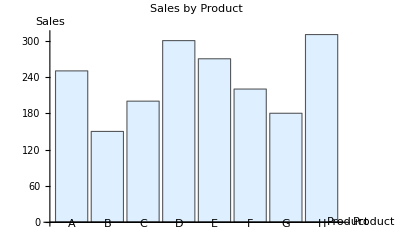

```mathematica
products=Rest[data][[All,1]];  
sales=Rest[data][[All,3]]; 
BarChart[sales,ChartLabels->products,ChartStyle->LightBlue,AxesLabel->{"Product","Sales"},PlotLabel->"Sales by Product"]
```

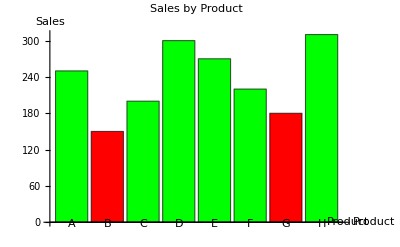

```mathematica
BarChart[sales,ChartLabels->products,ChartStyle->(If[#<200,Red,Green]&/@sales),
AxesLabel->{"Product","Sales"},PlotLabel->"Sales by Product"]
```

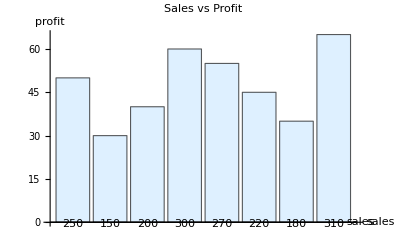

```mathematica
sales=Rest[data][[All,3]]; 
profit=Rest[data][[All,4]];
BarChart[profit,ChartLabels->sales,ChartStyle->LightBlue,AxesLabel->{"sales","profit"},PlotLabel->"Sales vs Profit"]
```

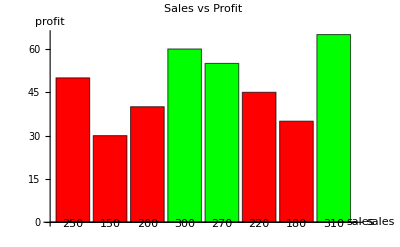

```mathematica
BarChart[profit,ChartLabels->sales,ChartStyle->(If[#>50,Green,Red]&/@profit),AxesLabel->{"sales","profit"},PlotLabel->"Sales vs Profit"]
```

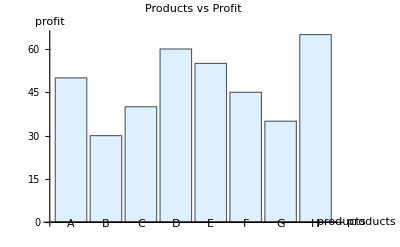

```mathematica
products=Rest[data][[All,1]]; 
profit=Rest[data][[All,4]];
BarChart[profit,ChartLabels->products,ChartStyle->LightBlue,AxesLabel->{"products","profit"},PlotLabel->"Products vs Profit"]
```

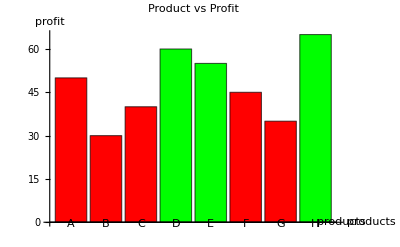

```mathematica
BarChart[profit,ChartLabels->products,ChartStyle->(If[#>50,Green,Red]&/@profit),AxesLabel->{"products","profit"},PlotLabel->"Product vs Profit"]
```